# 2 D

```mathematica
Needs["PlotLegends`"]
```

## Gaussian

```mathematica
rg0[L_,γ_]:=(1+(γ Gamma[2L+1])/(2^(2L-1)Factorial[L]Factorial[L+1]))^(1/4)
αg[L_,γ_]:=L/(√(8γ))
N[rg0[0,40]]
N[αg[0,40]]
N[rg0[1,40]]*√2
N[αg[1,40]]
N[rg0[2,40]]*√3
N[αg[2,40]]
N[rg0[4,40]]*√5
N[αg[4,40]]
```

3.

0.

3.0274

0.0559017

3.15434

0.111803

3.40471

0.223607

## TF - 0

```mathematica
r00[γ_]:=(64/3 γ)^(1/4)
R0[γ_,t_]:=r00[γ] √(1+t^2)
```

## TF - 2

```mathematica
Integrate[ρ^2(((L+1)(L+2))/(π R^(2L+2)))ρ^(2L)(1-ρ^2/R^2)ρ,{ϕ,0,2π},{ρ,0,R}]
```

((1+L) R^2)/(3+L)

```mathematica
ClearAll[C1,C2,C3,C4]
C1[L_]:=2/((L+1)(L+2));
C2[L_]:=2/((L+2)(L+3));
C3[L_]:=1/(2(L+1)(2L+1)(L+3));
C4[L_]:=4/(L(L+1));
```

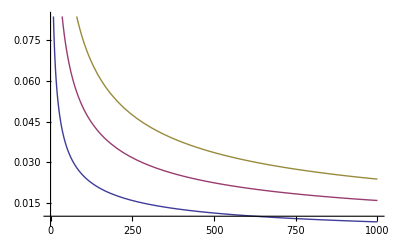

2.90392

0.

3.33025

0.0395285

3.73169

0.0790569

4.35834

0.158114

```mathematica
r20[L_,γ_]:=((L^2 C4[L]+32γ C3[L]/C1[L])C2[L]^-1)^(1/4)
rtf20[L_,γ_]:=((32γ C3[L]/C1[L])C2[L]^-1)^(1/4)
R2[L_,γ_,t_]:=r20[L,γ] √(1+t^2)
α2[L_,γ_]:=L/(4 √γ)
Plot[{1/(4 √γ),2/(4 √γ),3/(4 √γ)},{γ,0,1000}]
N[rtf20[0,40]*√(1/3)]
N[α2[0,40]]
N[r20[1,40]*√(2/4)]
N[α2[1,40]]
N[r20[2,40]*√(3/5)]
N[α2[2,40]]
N[r20[4,40]*√(5/7)]
N[α2[4,40]]
```

## TF - 1

```mathematica
ClearAll[A1,A2,A3,A4,DA1,DA2,DA3,DA4,DDA1,DDA2]
A1[L_,α_]:=1+2 L^2 α^2+2 L^2 α^2(1+2 L^2 α^2)Log[(L^2 α^2)/(1+L^2 α^2)];
DA10=4 L^2 α (3+Log[1-1/(1+L^2 α^2)]+4 L^2 Log[1-1/(1+L^2 α^2)] α^2-1/(1+L^2 α^2));
A2[L_,α_]:=1/3-L^2 α^2-2 L^4 α^4-2 L^4 α^4(1+L^2 α^2)Log[(L^2 α^2)/(1+L^2 α^2)];
DA20=-2 (L^2 α+2 L^4 (3+2 Log[1-1/(1+L^2 α^2)]) α^3+6 L^6 Log[1-1/(1+L^2 α^2)] α^5);
A3[L_,α_]:=1/6+2 L^2 α^2+2 L^4 α^4+L^2 α^2(1+3 L^2 α^2+2 L^4 α^4)Log[(L^2 α^2)/(1+L^2 α^2)];
DA30=2 L^2 α (3+Log[1-1/(1+L^2 α^2)]+6 L^2 α^2 (1+Log[1-1/(1+L^2 α^2)]+L^2 Log[1-1/(1+L^2 α^2)] α^2));
A4[L_,α_]:=2(1+α^2)(-1-(1+L^2 α^2)Log[(L^2 α^2)/(1+L^2 α^2)]);
DA40=2(-2-2 α^2 (2+(1+L^2) Log[1-1/(1+L^2 α^2)]+2 L^2 Log[1-1/(1+L^2 α^2)] α^2))/α;
A10=1+2 L^2 α^2+2 L^2 α^2(1+2 L^2 α^2)Log[(L^2 α^2)/(1+L^2 α^2)];
A20=1-L^2 α^2-2 L^4 α^4-2 L^4 α^4(1+L^2 α^2)Log[(L^2 α^2)/(1+L^2 α^2)];
A30=1/6+2 L^2 α^2+2 L^4 α^4+L^2 α^2(1+3 L^2 α^2+2 L^4 α^4)Log[(L^2 α^2)/(1+L^2 α^2)];
A40=2(1+α^2)(-1-(1+L^2 α^2)Log[(L^2 α^2)/(1+L^2 α^2)]);
A100=1;
A200=1/3;
A300=1/6;
A400=-2;
```

```mathematica
ClearAll[A1,A2,A3,A4]
A1=1+2(1+2Log[L α[t]])L^2 α[t];
A2=1/3-L^2 α[t]^2;
A3=1/6+2(1+Log[L α[t]])L^2 α[t]^2;
A4=-1-2Log[L α[t]]+(-1+L^2-2(1+L^2)Log[L α[t]])α[t]^2;
DA1=FullSimplify[D[A1,α[t]]];
DDA1=FullSimplify[D[A1,{α[t],2}]];
DA2=FullSimplify[D[A2,α[t]]];
DDA2=FullSimplify[D[A2,{α[t],2}]];
DA3=FullSimplify[D[A3,α[t]]];
DA4=FullSimplify[D[A4,α[t]]];
A10=1+2(1+2Log[L α0])L^2 α0;
A20=1/3-L^2 α0^2;
A30=1/6+2(1+Log[L α0])L^2 α0^2;
A40=-1-2Log[L α0]+(-1+L^2-2(1+L^2)Log[L α0])α0^2;
```

```mathematica
ClearAll[eq2R,eqs2R,eqe2R,eq2α,eqs2α,eqe2α]
R10[L_,α_,γ_]:=(1/A2[L,α](L^2 A4[L,α]+32γ A3[L,α]/A1[L,α]))^(1/4);
Rtf10[γ_]:=(1/A200(32γ A300/A100))^(1/4);
eq2α=32γ(3A20 A30 DA10/A10-DA30 A20-DA20 A30)==L^2(DA20 A40 A10+DA40 A20 A10-2DA10 A20 A40);
N[Rtf10[40]]
ss21=FindRoot[eq2α/.L->1/.γ->40,{α,0.0001}]
N[R10[1,α/.ss21,40]]
ss22=FindRoot[eq2α/.L->2/.γ->40,{α,0.0001}]
N[R10[2,α/.ss22,40]]
N[Rtf10[40]*√(A200/A100)]
ss21=FindRoot[eq2α/.L->1/.γ->40,{α,0.0001}]
N[R10[1,α/.ss21,40]*√(A2[1,α/.ss21]/A1[1,α/.ss21])]
ss22=FindRoot[eq2α/.L->2/.γ->40,{α,0.0001}]
N[R10[2,α/.ss22,40]*√(A2[2,α/.ss22]/A1[2,α/.ss22])]
ss24=FindRoot[eq2α/.L->4/.γ->40,{α,0.0001}]
N[R10[2,α/.ss24,40]*√(A2[2,α/.ss24]/A1[2,α/.ss24])]
```

5.02973

{α→0.0420909}

5.06412

{α→0.0395156}

5.15528

2.90392

{α→0.0420909}

2.94423

{α→0.0395156}

3.02931

{α→0.032925}

3.03322

## TF - 3

```mathematica
B1[L_,α_]:=√(1-4 L^2 α^2)-4 L^2 α^2 ArcTanh[√(1-4 L^2 α^2)]
B2[L_,α_]:=1/3 (1-4 L^2 α^2)^(3/2)
B3[L_,α_]:=1/6 (√(1-4 L^2 α^2)+8 L^2 α^2 √(1-4 L^2 α^2)-12 L^2 α^2 ArcTanh[√(1-4 L^2 α^2)])
B4[L_,α_]:=-4 (√(1-4 L^2 α^2)-ArcTanh[√(1-4 L^2 α^2)])
DB10=-8 L^2 α ArcTanh[√(1-4 L^2 α^2)];
DB20=-4 L^2 α √(1-4 L^2 α^2);
DB30=1/6 ((8 L^2 α)/(√(1-4 L^2 α^2))-(32 L^4 α^3)/(√(1-4 L^2 α^2))+16 L^2 α √(1-4 L^2 α^2)-24 L^2 α ArcTanh[√(1-4 L^2 α^2)]);
DB40=-4 (1/(α √(1-4 L^2 α^2))-(4 L^2 α)/(√(1-4 L^2 α^2)));
B10=√(1-4 L^2 α^2)-4 L^2 α^2 ArcTanh[√(1-4 L^2 α^2)];
B20=1/3 (1-4 L^2 α^2)^(3/2);
B30=1/6 (√(1-4 L^2 α^2)+8 L^2 α^2 √(1-4 L^2 α^2)-12 L^2 α^2 ArcTanh[√(1-4 L^2 α^2)]);
B40=-4 (√(1-4 L^2 α^2)-ArcTanh[√(1-4 L^2 α^2)]);
B100=1;
B200=1/3;
B300=1/6;
```

```mathematica
ClearAll[eq3R,eqs3R,eqe3R,eq3α,eqs3α,eqe3α]
R30[L_,α_,γ_]:=(1/B2[L,α](L^2 B4[L,α]+32γ B3[L,α]/B1[L,α]))^(1/4);
Rtf30[γ_]:=(1/B200(32γ B300/B100))^(1/4);
eq3α=32γ(3B20 B30 DB10/B10-DB30 B20-DB20 B30)==L^2(DB20 B40 B10+DB40 B20 B10-2DB10 B20 B40);
N[Rtf30[4000]*√(B200/B100)]
ss31=FindRoot[eq3α/.L->1/.γ->4000,{α,0.0001}]
N[R30[1,α/.ss31,4000]*√(B2[1,α/.ss31]/B1[1,α/.ss31])]
ss32=FindRoot[eq3α/.L->2/.γ->4000,{α,0.0001}]
N[R30[2,α/.ss32,4000]*√(B2[2,α/.ss32]/B1[2,α/.ss32])]
ss34=FindRoot[eq3α/.L->4/.γ->40,{α,0.0001}]
N[R30[2,α/.ss34,40]*√(B2[2,α/.ss34]/B1[2,α/.ss34])]
```

9.183

{α→0.0039521}

9.18516

{α→0.00395021}

9.19047

{α→0.0354355}

3.0162

```mathematica
Solve[1-(L^2 α^2)/ρ^2-ρ^2==0,ρ]
```

{{ρ→-(√(1-√(1-4 L^2 α^2)))/(√2)},{ρ→(√(1-√(1-4 L^2 α^2)))/(√2)},{ρ→-(√(1+√(1-4 L^2 α^2)))/(√2)},{ρ→(√(1+√(1-4 L^2 α^2)))/(√2)}}

```mathematica
Solve[R^2*Integrate[((2ν)/(π R^2 A1))(1-(L^2 α^2)/ρ^2-ρ^2)ρ,{ϕ,0,2π},{ρ,(√(1-√(1-4 L^2 α^2)))/(√2),(√(1+√(1-4 L^2 α^2)))/(√2)}]==ν,A1]
```

{{A1→√(1-4 L^2 α^2)-4 L^2 α^2 ArcTanh[√(1-4 L^2 α^2)]}}

```mathematica
Solve[(ℏ DB)/2 R^4*Integrate[((2ν)/(π R^2 A1))ρ^2(1-(L^2 α^2)/ρ^2-ρ^2)ρ,{ϕ,0,2π},{ρ,(√(1-√(1-4 L^2 α^2)))/(√2),(√(1+√(1-4 L^2 α^2)))/(√2)}]==(ℏ ν DB R^2 A2)/(2A1),A2]
```

{{A2→1/3 (1-4 L^2 α^2)^(3/2)}}

```mathematica
R^2*Integrate[((2ν)/(π R^2 A1))^2(1-(L^2 α^2)/ρ^2-ρ^2)^2 ρ,{ϕ,0,2π},{ρ,(√(1-√(1-4 L^2 α^2)))/(√2),(√(1+√(1-4 L^2 α^2)))/(√2)}]
```

(4 ν^2 (√(1-4 L^2 α^2) (1+8 L^2 α^2)-12 L^2 α^2 ArcTanh[√(1-4 L^2 α^2)]))/(3 A1^2 π R^2)

```mathematica
Solve[U/2 R^2*Integrate[((2ν)/(π R^2 A1))^2(1-(L^2 α^2)/ρ^2-ρ^2)^2 ρ,{ϕ,0,2π},{ρ,(√(1-√(1-4 L^2 α^2)))/(√2),(√(1+√(1-4 L^2 α^2)))/(√2)}]==(4U ν^2 A3)/(π R^2 A1^2),A3]
```

{{A3→1/6 (√(1-4 L^2 α^2)+8 L^2 α^2 √(1-4 L^2 α^2)-12 L^2 α^2 ArcTanh[√(1-4 L^2 α^2)])}}

```mathematica
Solve[ℏ^2/(2m)L^2*Integrate[((2ν)/(π R^2 A1))1/ρ^2(1-(L^2 α^2)/ρ^2-ρ^2)ρ,{ϕ,0,2π},{ρ,(√(1-√(1-4 L^2 α^2)))/(√2),(√(1+√(1-4 L^2 α^2)))/(√2)}]==(L^2 ℏ^2 ν A4)/(2 R^2 m A1),A4]
```

{{A4→-4 (√(1-4 L^2 α^2)-ArcTanh[√(1-4 L^2 α^2)])}}

## Expansão (Poster Quo Vadis)

L = 0

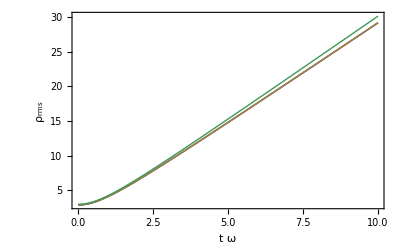

```mathematica
fTF2[t_]:=2.9039 √(1+t^2)
fTF3[t_]:=2.9039 √(1+t^2)
fTF1[t_]:=2.9039 √(1+t^2)
fG[t_]:=3 √(1+t^2)
g0=Plot[{fTF1[t],fTF2[t],fTF3[t],fG[t]},{t,0,10},RotateLabel->False,FrameLabel->{t*ω,Subscript[ρ,rms]},PlotRange->All,Frame->True,Axes->False,PlotLegend->{Subscript[Ψ,0]^("(1)"),Subscript[Ψ,0]^("(2)"),Subscript[Ψ,0]^("(3)"),Subscript[Ψ,0]^("(4)")},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
```

L = 1

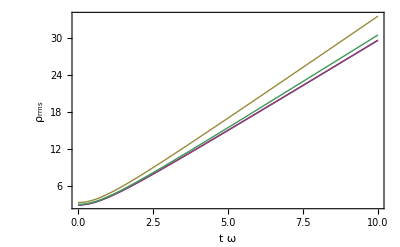

```mathematica
fTF2[t_]:=2.9442 √(1+t^2)
fTF3[t_]:=3.3302 √(1+t^2)
fTF1[t_]:=2.9412 √(1+t^2)
fG[t_]:=3.0274 √(1+t^2)
g1=Plot[{fTF1[t],fTF2[t],fTF3[t],fG[t]},{t,0,10},RotateLabel->False,FrameLabel->{t*ω,Subscript[ρ,rms]},PlotRange->All,Frame->True,Axes->False,PlotLegend->{Subscript[Ψ,1]^("(1)"),Subscript[Ψ,1]^("(2)"),Subscript[Ψ,1]^("(3)"),Subscript[Ψ,1]^("(4)")},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
```

L = 2

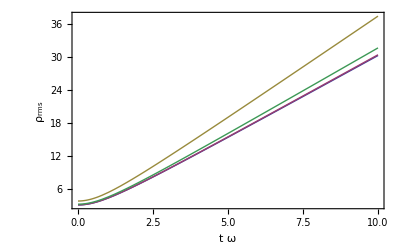

```mathematica
fTF2[t_]:=3.0293 √(1+t^2)
fTF3[t_]:=3.7317 √(1+t^2)
fTF1[t_]:=3.0160 √(1+t^2)
fG[t_]:=3.1543 √(1+t^2)
g2=Plot[{fTF1[t],fTF2[t],fTF3[t],fG[t]},{t,0,10},RotateLabel->False,FrameLabel->{t*ω,Subscript[ρ,rms]},PlotRange->All,Frame->True,Axes->False,PlotLegend->{Subscript[Ψ,2]^("(1)"),Subscript[Ψ,2]^("(2)"),Subscript[Ψ,2]^("(3)"),Subscript[Ψ,2]^("(4)")},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.8},LegendShadow->{0,0}]
```

L = 4

```mathematica
fTF2[t_]:=4.0004 √(1+t^2)
fTF3[t_]:=4.3584 √(1+t^2)
fTF1[t_]:=3.0162 √(1+t^2)
fG[t_]:=3.4047 √(1+t^2)
g4=Plot[{fTF1[t],fTF2[t],fTF3[t],fG[t]},{t,0,10},RotateLabel->False,FrameLabel->{t*ω,Subscript[ρ,rms]},PlotRange->All,Frame->True,Axes->False,PlotLegend->{Subscript[Ψ,4]^("(1)"),Subscript[Ψ,4]^("(2)"),Subscript[Ψ,4]^("(3)"),Subscript[Ψ,4]^("(4)")},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.8},LegendShadow->{0,0}]
```

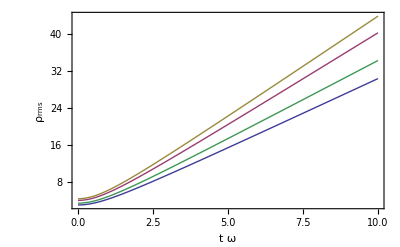

```mathematica
Export["Dropbox/Artigos/1/1-2D-fig0.eps",g0]
Export["Dropbox/Artigos/1/1-2D-fig1.eps",g1]
Export["Dropbox/Artigos/1/1-2D-fig2.eps",g2]
```

Dropbox/Artigos/1/1-2D-fig0.eps

Dropbox/Artigos/1/1-2D-fig1.eps

Dropbox/Artigos/1/1-2D-fig2.eps

## Energias (Poster Quo Vadis)

### TF1

```mathematica
D1[L_,α_]:=(1/3(1-4 L^2 α^2)^(3/2))/(√(1-4 L^2 α^2)-4 L^2 α^2 ArcTan[√(1-4 L^2 α^2)])
D2[L_,α_]:=(4ArcTan[√(1-4 L^2 α^2)]-4 √(1-4 L^2 α^2))/(√(1-4 L^2 α^2)-4 L^2 α^2 ArcTan[√(1-4 L^2 α^2)])
D3[L_,α_]:=(1/6(1+8 L^2 α^2)√(1-4 L^2 α^2)-2 L^2 α^2 ArcTan[√(1-4 L^2 α^2)])/((√(1-4 L^2 α^2)-4 L^2 α^2 ArcTan[√(1-4 L^2 α^2)])^2)
ETF1[L_,γ_,u_,α_]:=D1[L,α]/2 u^2+((L^2 D2[L,α])/2+16D3[L,α] γ)(1/u^2)
ETF1[0,40,5.0297,0]
ETF1[1,40,5.0589,0.0391]
ETF1[2,40,5.1236,0.0381]
```

8.51767

8.45496

8.43274

8.51767

8.45496

8.43274

8.43274

8.45496

8.51767

### TF2

```mathematica
C1[L_,α_]:=(1/3-L^2 α^2-2 L^4 α^4-2 L^4 α^4(1+L^2 α^2)Log[(L^2 α^2)/(1+L^2 α^2)])/(1+2 L^2 α^2+2 L^2 α^2(1+2 L^2 α^2)Log[(L^2 α^2)/(1+L^2 α^2)])
C2[L_,α_]:=(2(1+α^2)(-1-(1+L^2 α^2)Log[(L^2 α^2)/(1+L^2 α^2)]))/(1+2 L^2 α^2+2 L^2 α^2(1+2 L^2 α^2)Log[(L^2 α^2)/(1+L^2 α^2)])
C3[L_,α_]:=(1/6+2 L^2 α^2+2 L^4 α^4+L^2 α^2(1+3 L^2 α^2+2 L^4 α^4)Log[(L^2 α^2)/(1+L^2 α^2)])/((1+2 L^2 α^2+2 L^2 α^2(1+2 L^2 α^2)Log[(L^2 α^2)/(1+L^2 α^2)])^2)
ETF2[L_,γ_,u_,α_]:=C1[L,α]/2 u^2+((L^2 C2[L,α])/2+16C3[L,α] γ)(1/u^2)
ETF20[γ_,u_]:=1/6 u^2+(16/6 γ)(1/u^2)
ETF20[40,5.0297]
ETF2[1,40,5.0641,0.0421]
ETF2[2,40,5.1553,0.0395]
```

9.17677

8.66848

8.43274

9.17677

8.66848

8.43274

8.43274

8.66848

9.17677

### TF3

```mathematica
F1[L_]:=(2(L+1)(L+2))/(2(L+2)(L+3))
F2[L_]:=(4(L+1)(L+2))/(2L(L+1))
F3[L_]:=((L+1)(L+2))^2/(8(L+1)(2L+1)(L+3))
ETF3[L_,γ_,u_]:=F1[L]/2 u^2+((L^2 F2[L])/2+16F3[L] γ)(1/u^2)
ETF30[L_,γ_,u_]:=F1[L]/2 u^2+(16F3[L] γ)(1/u^2)
ETF30[0,40,5.0297]
ETF3[1,40,4.7097]
ETF3[2,40,4.8176]
```

13.9255

11.0905

8.43274

13.9255

11.0905

8.43274

8.43274

11.0905

13.9255

### Gaussian

```mathematica
Integrate[r^(2 L)Exp[-r^2/R^2]r,{r,0,∞},{ϕ,0,2π},Assumptions->Re[L]>0&&Re[R^2]>0]
```

π (1/R^2)^-L R^2 Gamma[1+L]

π (1/R^2)^-L R^2 Gamma[1+L]

π (1/R^2)^-L R^2 Gamma[1+L]

```mathematica
ℏ^2/(2m)Integrate[FullSimplify[D[√(ν/(π R^(2L+2)Gamma[1+L]))r^L Exp[-r^2/(2 R^2)] ⅇ^(ⅈ L ϕ),r]D[√(ν/(π R^(2L+2)Gamma[1+L]))r^L Exp[-r^2/(2 R^2)] ⅇ^(-ⅈ L ϕ),r]+1/r^2 D[√(ν/(π R^(2L+2)Gamma[1+L]))r^L Exp[-r^2/(2 R^2)] ⅇ^(ⅈ L ϕ),ϕ]D[√(ν/(π R^(2L+2)Gamma[1+L]))r^L Exp[-r^2/(2 R^2)] ⅇ^(-ⅈ L ϕ),ϕ]]r,{r,0,∞},{ϕ,0,2π},Assumptions->Re[L]>0&&Re[R^2]>0]+1/2 m ω^2 Integrate[r^2 √(ν/(π R^(2L+2)Gamma[1+L]))r^L Exp[-r^2/(2 R^2)] ⅇ^(-ⅈ L ϕ)√(ν/(π R^(2L+2)Gamma[1+L]))r^L Exp[-r^2/(2 R^2)] ⅇ^(ⅈ L ϕ)r,{r,0,∞},{ϕ,0,2π},Assumptions->Re[L]>0&&Re[R^2]>0]+U/2 Integrate[(√(ν/(π R^(2L+2)Gamma[1+L]))r^L Exp[-r^2/(2 R^2)])^4 r,{r,0,∞},{ϕ,0,2π},Assumptions->Re[L]>0&&Re[R^2]>0]
```

1/2 (1+L) m (1/R^2)^-L R^(2-2 L) ν ω^2+((1+L) (1/R^2)^(1-L) R^(-2 L) ν ℏ^2)/(2 m)+(2^(-2-2 L) (1/R^2)^(1-2 L) R^(-4 L) U ν^2 Gamma[1+2 L])/(π Gamma[1+L]^2)

1/2 (1+L) m (1/R^2)^-L R^(2-2 L) ν ω^2+((1+L) (1/R^2)^(1-L) R^(-2 L) ν ℏ^2)/(2 m)+(2^(-2-2 L) (1/R^2)^(1-2 L) R^(-4 L) U ν^2 Gamma[1+2 L])/(π Gamma[1+L]^2)

1/2 (1+L) m (1/R^2)^-L R^(2-2 L) ν ω^2+((1+L) (1/R^2)^(1-L) R^(-2 L) ν ℏ^2)/(2 m)+(2^(-2-2 L) (1/R^2)^(1-2 L) R^(-4 L) U ν^2 Gamma[1+2 L])/(π Gamma[1+L]^2)

```mathematica
Limit[(γ Factorial[2L])/(2^(2L)√(2π)Factorial[L]^2 r^2 z),L->∞]
Limit[(γ √(2π 2L)((2L)/ⅇ)^(2L))/(2^(2L)√(2π)(√(2π L)(L/ⅇ)^L)^2 r^2 z),L->∞]
FullSimplify[(γ √(2π 2L)((2L)/ⅇ)^(2L))/(2^(2L)√(2π)(√(2π L)(L/ⅇ)^L)^2 r^2 z)]
```

γ/(√2 √L π r^2 z)

0

0

γ/(√2 √L π r^2 z)

0

0

0

«1 more identical outputs»

γ/(√2 √L π r^2 z)

```mathematica
Eg[L_,γ_,u_]:=1/2(L+1)(u^2+1/u)+(γ Factorial[2L])/(2^(2L)u^2 Factorial[L]^2)
```

```mathematica
N[Eg[0,40,3]]
Eg[1,40,2.1407]
Eg[2,40,1.8212]
```

10.3213

9.41407

9.11111

10.3213

9.41407

9.11111

9.11111

9.41407

10.3213

```mathematica
N[4/3 40^(1/2)]
N[Log[3.55 40^(1/2)]/(2 40^(1/2))]
N[4/3 40^(1/2)+Log[13 40]/(3 40^(1/2))]
```

8.76235

0.245977

8.43274

8.76235

0.245977

8.43274

8.43274

0.245977

8.76235

### Razão

```mathematica
ETF20[4000,15.9054]/ETF1[0,4000,15.9054,0]
ETF2[1,4000,15.9068,0.0043]/ETF1[1,4000,15.9069,0.004]
ETF2[2,4000,15.9106,0.0043]/ETF1[2,4000,15.9107,0.004]
```

1.

1.00046

1.0016

```mathematica
ETF30[0,4000,15.9054]/ETF1[0,4000,15.9054,0]
ETF3[1,4000,14.8026]/ETF1[1,4000,15.9069,0.004]
ETF3[2,4000,15.0444]/ETF1[2,4000,15.9107,0.004]
```

1.

1.29916

1.61021

```mathematica
N[Eg[0,4000,9.4577]]/ETF1[0,4000,15.9054,0]
Eg[1,4000,6.6882]/ETF1[1,4000,15.9069,0.004]
Eg[2,4000,5.6248]/ETF1[2,4000,15.9107,0.004]
```

1.06129

1.0624

1.12804